# Plots of Experiment Results

```mathematica
ClearAll
```

ClearAll

## Functions to Generate Pretty Plots

### 3D Plot

```mathematica
Clear[plotExperimentResults];
plotExperimentResults[alg_,initSolType_,k_,realizations_,seed_,currentDir_,nList_,mList_,scheduleToTest_]:=plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]=Module[
(* Put local variables here *)
{makespanGapDataPath,runtimeDataPath,makespanGapRawData,runtimeRawData,makespanGapData,runtimeData,index},

Clear[makespanGapDataPath,runtimeDataPath,makespanGapRawData,runtimeRawData,makespanGapData,runtimeData,index];

(* Define data to import *)
If [scheduleToTest== "Simple"||scheduleToTest== "LinMult"||scheduleToTest== "QuadMult"||scheduleToTest== "ExpMult",
If[seed==1,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,scheduleToTest]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,scheduleToTest]];,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,scheduleToTest]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,scheduleToTest]];
],
If[seed==1,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_seeded.csv",alg,initSolType,k,realizations]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_seeded.csv",alg,initSolType,k,realizations]];,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_noSeed.csv",alg,initSolType,k,realizations]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_noSeed.csv",alg,initSolType,k,realizations]];
]
];

(* Import the data *)
Print["Searching for data files at\n\t",makespanGapDataPath];
makespanGapRawData=Import[makespanGapDataPath];
runtimeRawData=Import[runtimeDataPath];

(* Initialize plot data *)
makespanGapData=ConstantArray[0,{(Length[nList])*Length[mList]}];
runtimeData=ConstantArray[0,{(Length[nList])*Length[mList]}];

(* Process data into an easily plottable form *)
For[i=1,i≤Length[mList],i++,
For[j=1,j≤Length[nList],j++,
index=(i-1)*Length[nList]+j;
makespanGapData⟦index⟧={mList⟦i⟧,nList⟦j⟧,makespanGapRawData⟦i,j⟧};
runtimeData⟦index⟧={mList⟦i⟧,nList⟦j⟧,runtimeRawData⟦i,j⟧};
];
];

(* Plot makespan gap as a percentage between 0 and 20 *)
ListPlot3D[makespanGapData,Mesh->All,AxesLabel->{"Machines","Jobs","Makespan Gap\n(percentage)"},ImageSize->400,PlotRange->{0,20},ColorFunction->"TemperatureMap",ViewPoint->{3,2,1}]

(* Plot runtime in between 0 and 1200 (20 mins) *)
ListPlot3D[runtimeData,Mesh->All,AxesLabel->{"Machines","Jobs","Run-time\n(seconds)"},ImageSize->400,PlotRange->{0,1200},ColorFunction->"TemperatureMap",ViewPoint->{3,2,1}]

];
```

### Loglog Plot

```mathematica
Clear[plotExperimentResultsLoglog];
plotExperimentResultsLoglog[alg_,initSolType_,k_,realizations_,seed_,currentDir_,nList_,mList_,dist_,plotColour_]:=plotExperimentResultsLoglog[alg,initSolType,k,realizations,seed,currentDir,nList,mList,dist,plotColour]=Module[
(* Put local variables here *)
{makespanGapDataPath,runtimeDataPath,makespanGapRawData,runtimeRawData,makespanGapData,runtimeData,index},

Clear[makespanGapRawData,runtimeRawData,makespanGapData,
runtimeData,index];

(* Define data to import *)
If[seed==1,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,dist]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_seeded_``.csv",alg,initSolType,k,realizations,dist]];,
makespanGapDataPath=currentDir<>ToString[StringForm["data/makespanGap_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,dist]];
runtimeDataPath=currentDir<>ToString[StringForm["data/runtime_``_``_k``-``_noSeed_``.csv",alg,initSolType,k,realizations,dist]];
];

(* Import the data *)
Print["Searching for data files at\n\t",runtimeDataPath];
makespanGapRawData=Import[makespanGapDataPath]⟦1⟧;
runtimeRawData=Import[runtimeDataPath]⟦1⟧;

(* Initialize plot data *)
makespanGapData=ConstantArray[0,Length[nList]];
runtimeData=ConstantArray[0,Length[nList]];

(* Process data into an easily plottable form *)
For[j=1,j≤Length[nList],j++,
makespanGapData⟦j⟧={nList⟦j⟧,makespanGapRawData⟦j⟧};
runtimeData⟦j⟧={nList⟦j⟧,runtimeRawData⟦j⟧};
];

(* Plot makespan gap as a percentage between 0 and 20 *)
marker1=Graphics[{plotColour,Disk[]}];
ListLogLogPlot[makespanGapData,AxesLabel->{"Jobs","Makespan Gap\n(percentage)"},ImageSize->400,Ticks->Automatic,Joined->True,PlotMarkers->{●,10},PlotStyle->{plotColour},PlotLegends->{dist}]

(* Plot runtime in between 0 and 300 (5 mins) *)
ListLogLogPlot[runtimeData,AxesLabel->{"Jobs","Run-time\n(seconds)"},ImageSize->400,Ticks->Automatic,Joined->True,PlotMarkers->{●,10},PlotStyle->{plotColour},PlotLegends->{dist}]
];
```

## Question 1

### Part (c) Determining k

Here we test GLS for varying values of k for both random and GMS initial solutions in order to determine our k-value. We use randomly generated input instances.

#### k=1

```mathematica
k=1;
alg="GLS";
initSolType="random";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k1-20_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=1;
alg="GLS";
initSolType="GMS";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k1-1_noSeed.csv

-Graphics3D- -Graphics3D-

#### k=2

```mathematica
k=2;
alg="GLS";
initSolType="random";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k2-1_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="GLS";
initSolType="GMS";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_GLS_GMS_k2-1_noSeed.csv

-Graphics3D- -Graphics3D-

#### k=3

```mathematica
k=3;
alg="GLS";
initSolType="random";
realizations=1;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k3-1_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=3;
alg="GLS";
initSolType="GMS";
realizations=1;
seed=0;
nList={10,20,30,40};
mList={2,3,4,5};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k3-1_noSeed.csv

-Graphics3D- -Graphics3D-

### Part (d) Testing the performance of GLS

Using a seed, we generate a set of input instances to the makespan scheduling problem. We run GLS on this set of instances using the k-value found in part (c) to determine the limits of our GLS algorithm. We decided a “reasonable” upper limit on the runtime of the algorithm was 5 minutes. Using both random and GMS initial solutions, we compare the results of these tests:

```mathematica
k=2;
alg="GLS";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_random_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="GLS";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_GLS_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

## Question 2

### Part (c) Testing the performance of VDS

```mathematica
k=2;
alg="VDS";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_VDS_random_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="VDS";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_VDS_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

## Question 3

### Testing simulated annealing with random and GMS initial solutions

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="NA";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_GMS_k2-10_seeded.csv

-Graphics3D- -Graphics3D-

### Testing simulated annealing with each of the 4 cooling schedules

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="Simple";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_Simple.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="LinMult";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_LinMult.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="QuadMult";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_QuadMult.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=10;
seed=1;
nList={10,20,30,40,50,60,70,80,90,100};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
scheduleToTest="ExpMult";
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList,scheduleToTest]
```

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/makespanGap_Ours_random_k2-10_seeded_ExpMult.csv

-Graphics3D- -Graphics3D-

### Testing the limits of Simulated Annealing

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/runtime_Ours_GMS_k2-10_seeded_uniform.csv

Searching for data files at
	/Users/kdyoung/AAH-makespanScheduling/data/runtime_Ours_GMS_k2-10_seeded_fatTailed.csv

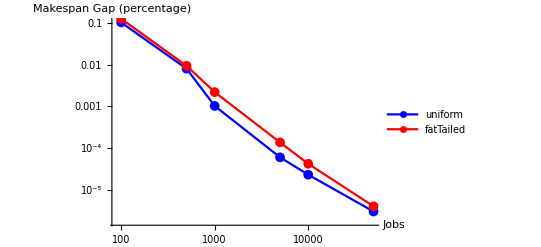

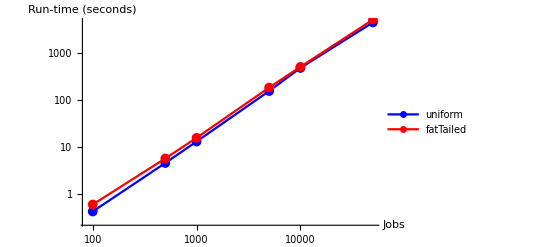

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=10;
seed=1;
nList={100,500,1000,5000,10000,50000};
mList={2};
currentDir=NotebookDirectory[];

dist="uniform";
plotsUniform=plotExperimentResultsLoglog[alg,initSolType,k,realizations,seed,currentDir,nList,mList,dist,Blue];

dist="fatTailed";
plotsFatTailed=plotExperimentResultsLoglog[alg,initSolType,k,realizations,seed,currentDir,nList,mList,dist,Red];

(* Plot results on the same axis to compare the results *)
Show[plotsUniform⟦1⟧,plotsFatTailed⟦1⟧] 
Show[plotsUniform⟦2⟧,plotsFatTailed⟦2⟧]
```

### Misc. Heuristic Plots

#### k=2: Compare random and GMS

```mathematica
k=2;
alg="Ours";
initSolType="random";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_random_k2-20_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_GMS_k2-20_noSeed.csv

-Graphics3D- -Graphics3D-

#### k=3: Compare random and GMS

```mathematica
k=3;
alg="Ours";
initSolType="random";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_random_k3-20_noSeed.csv

-Graphics3D- -Graphics3D-

```mathematica
k=3;
alg="Ours";
initSolType="GMS";
realizations=20;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_GMS_k3-20_noSeed.csv

-Graphics3D- -Graphics3D-

#### k=2: Testing parameter values

```mathematica
k=2;
alg="Ours";
initSolType="GMS";
realizations=2;
seed=0;
nList={15,20,25,30,35,40,45,50};
mList={2,4,6,8,10};
currentDir=NotebookDirectory[];
plotExperimentResults[alg,initSolType,k,realizations,seed,currentDir,nList,mList]
```

Searching for data files at
	/Users/pamelajenkins/Documents/Lotte/Approximation Algorithms/AAH-makespanScheduling-master/data/makespanGap_Ours_GMS_k2-2_noSeed.csv

Import::nffil: File not found during Import.

Part::partd: Part specification $Failed⟦1,1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics3D- -Graphics3D-